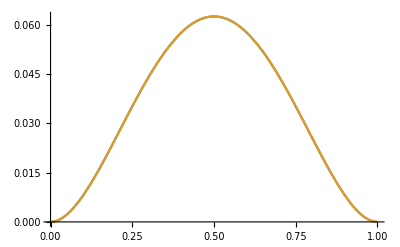

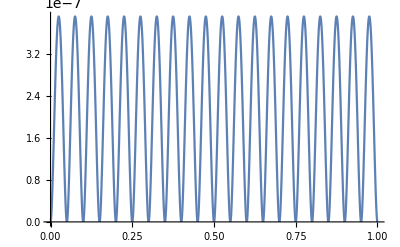

```mathematica
(* f(t) = t / (1 + t^2) с интерполационни възли x[k] = k / n, k = 0,1,.......,n *)
n=20;
Do[x[k]=k/n,{k,0,n}];
f[t_]:=(t^2)*(1-t)^2;

(* Тъй като възлите са равноотдалечени, то Δi = Xi+1 - Xi е едно и също число, а именно 1/n *)
delta=1/n;

(* Sn(x) се нарича пълна кубична интерполанта при този избор на d[0] и d[n] *)
d[0]=f'[x[0]];
d[n]=f'[x[n]];

(* Генерираме полиномите във всеки един от възлите *)
P[i_,t_]:=f[x[i]]+d[i]*(t-x[i])+(((f[x[i+1]]-f[x[i]])/delta-d[i])/delta)*(t-x[i])^2+((d[i+1]-2*(f[x[i+1]]-f[x[i]])/delta+d[i])/delta^2)*(t-x[i])^2*(t-x[i+1]);

(* Намираме сплайн функцията Sn *)
Sn[t_]:=Sum[If[t≥x[i]&&t≤x[i+1],P[i,t],0],{i,0,n-1}];

(* Дефинираме коефициентите в тридиагоналната матрица *)
a=1/delta;
b=2*(1/delta+1/delta);
c=1/delta;

(* Дефинираме десните страни на уравненията в тридиагоналната матрица *)
Do[r[i]=3*((f[x[i]]-f[x[i-1]])/(delta^2)+(f[x[i+1]]-f[x[i]])/(delta^2)),{i,1,n-1}];

(* Начална инициализация на α1 и β1 *)
alpha[1]=-c/b;
beta[1]=r[1]/b;

(* Метод на прогонката - прав ход *)
Do[{alpha[k]=-c/(a*alpha[k-1]+b),beta[k]=(r[k]-a*beta[k-1])/(a*alpha[k-1]+b)},{k,2,n-1}];

(* Метод на прогонката - обратен ход *)
Do[d[k]=alpha[k]*d[k+1]+beta[k],{k,n-1,1,-1}];

Plot[{f[t],Sn[t]},{t,0,1},PlotRange->All] (* Едновременно визуализиране на графиките на f[t] и Sn[t] в интервала [0,1] *)
Plot[f[t]-Sn[t],{t,0,1},PlotRange->All] (* Визуализиране на графиката на f[t] - Sn[t] в интервала [0,1] *)
```

```mathematica
f[k_]:=k^3*(k+2)^3;
g[k_]:=k^2*(k+2)^2;
Sum[f[k],{k,1,21,2}] + Sum[g[k],{k,2,22,2}]
```

238872205